```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["Results.xlsx"][[1]];
sNames=s[[1]]
sData=s[[2;;]]
sData[[;;,1]]
```

{p,L,w,I,var(I),Pfail}

{{0.01,3.,2.,0.0144685,1.82×10^-8,0.0023866},{0.01,3.,3.,0.233588,9.51×10^-8,0.0584726},{0.01,5.,2.,0.00291345,3.88×10^-9,0.0002779},{0.01,5.,3.,0.020458,2.92×10^-8,0.0049434},{0.01,5.,4.,0.550399,8.31×10^-8,0.139494},{0.01,5.,5.,0.501635,7.89×10^-8,0.182},{0.01,7.,2.,0.000389362,5.81×10^-10,0.0000248},{0.01,7.,3.,0.0368854,2.68×10^-8,0.0043856},{0.01,7.,4.,0.0431134,4.85×10^-8,0.0119192},{0.01,7.,5.,0.6459,6.69×10^-8,0.19352},{0.01,9.,2.,0.0000335,6.02×10^-11,1.6×10^-6},{0.01,9.,3.,0.00519944,5.39×10^-9,0.0004316},{0.01,9.,4.,0.0685862,4.34×10^-8,0.0099234},{0.01,9.,5.,0.106705,7.32×10^-8,0.0288206},{0.01,11.,2.,7.32×10^-6,1.49×10^-11,3.×10^-7},{0.01,11.,3.,0.000989499,1.29×10^-9,0.0000671},{0.01,11.,4.,0.0138206,1.24×10^-8,0.001379},{0.01,11.,5.,0.124453,6.43×10^-8,0.0216369},{0.02,3.,2.,0.040401,4.22×10^-8,0.0090975},{0.02,3.,3.,0.335684,1.×10^-7,0.114347},{0.02,5.,2.,0.0152947,1.7×10^-8,0.0021644},{0.02,5.,3.,0.061015,6.45×10^-8,0.020639},{0.02,5.,4.,0.732671,4.49×10^-8,0.260581},{0.02,5.,5.,0.58834,3.11×10^-8,0.332308},{0.02,7.,2.,0.00490945,5.14×10^-9,0.0004054},{0.02,7.,3.,0.109603,7.14×10^-8,0.0177189},{0.02,7.,4.,0.10981,8.95×10^-8,0.0480967},{0.02,7.,5.,0.772886,1.87×10^-8,0.354685},{0.02,9.,2.,0.001078,1.35×10^-9,0.0000713},{0.02,9.,3.,0.0324689,2.41×10^-8,0.0037178},{0.02,9.,4.,0.177667,8.45×10^-8,0.0397169},{0.02,9.,5.,0.25588,9.13×10^-8,0.106594},{0.02,11.,2.,0.000241478,3.57×10^-10,0.0000137},{0.02,11.,3.,0.00975441,8.76×10^-9,0.0008404},{0.02,11.,4.,0.0809034,4.51×10^-8,0.0106701},{0.02,11.,5.,0.352978,9.23×10^-8,0.082109},{0.03,3.,2.,0.0687321,6.35×10^-8,0.0195028},{0.03,3.,3.,0.386078,9.03×10^-8,0.166826},{0.03,5.,2.,0.0381754,3.55×10^-8,0.006912},{0.03,5.,3.,0.108745,8.89×10^-8,0.0474813},{0.03,5.,4.,0.782603,1.68×10^-8,0.365014},{0.03,5.,5.,0.567242,6.93×10^-9,0.456373},{0.03,7.,2.,0.0204167,1.66×10^-8,0.0021051},{0.03,7.,3.,0.232023,1.59×10^-7,0.0420669},{0.03,7.,4.,0.168043,1.02×10^-7,0.10652},{0.03,7.,5.,0.73829,2.24×10^-9,0.486653},{0.03,9.,2.,0.00736947,6.94×10^-9,0.000608},{0.03,9.,3.,0.0985687,5.06×10^-8,0.0132858},{0.03,9.,4.,0.165948,2.6×10^-7,0.0889478},{0.03,9.,5.,0.126791,3.57×10^-7,0.212819},{0.03,11.,2.,0.00267874,2.96×10^-9,0.0001945},{0.03,11.,3.,0.0406386,2.68×10^-8,0.0043919},{0.03,11.,4.,0.209745,7.75×10^-8,0.0352474},{0.03,11.,5.,0.5914,7.16×10^-8,0.17755},{0.04,3.,2.,0.0952392,8.03×10^-8,0.0329654},{0.04,3.,3.,0.40928,7.57×10^-8,0.217011},{0.04,5.,2.,0.0663113,5.58×10^-8,0.0155447},{0.04,5.,3.,0.154669,9.82×10^-8,0.0844252},{0.04,5.,4.,0.764309,4.×10^-9,0.455165},{0.04,5.,5.,0.506966,5.3×10^-9,0.557994},{0.04,7.,2.,0.0456356,3.41×10^-8,0.0064798},{0.04,7.,3.,0.286019,9.13×10^-8,0.0727297},{0.04,7.,4.,0.212208,9.13×10^-8,0.182548},{0.04,7.,5.,0.642703,8.88×10^-9,0.593039},{0.04,9.,2.,0.0266794,1.95×10^-8,0.0026711},{0.04,9.,3.,0.20565,7.59×10^-8,0.0331808},{0.04,9.,4.,0.521695,7.77×10^-8,0.157495},{0.04,9.,5.,0.929065,0.000041,0.335511},{0.04,11.,2.,0.0132545,,0.0011877},{0.04,11.,3.,0.112697,,0.0150664},{0.04,11.,4.,0.402579,9.14×10^-8,0.082189},{0.04,11.,5.,0.719072,4.02×10^-8,0.292143},{0.05,3.,2.,0.118329,9.23×10^-8,0.0490965},{0.05,3.,3.,0.413209,6.04×10^-8,0.264802},{0.05,5.,2.,0.0940052,7.44×10^-8,0.0284723},{0.05,5.,3.,0.193342,9.37×10^-8,0.129787},{0.05,5.,4.,0.709774,3.17×10^-9,0.533238},{0.05,5.,5.,0.43476,1.72×10^-8,0.641443},{0.05,7.,2.,0.0849682,5.56×10^-8,0.0151285},{0.05,7.,3.,0.264034,1.45×10^-7,0.115548},{0.05,7.,4.,0.225287,7.78×10^-8,0.270285},{0.05,7.,5.,0.529971,2.68×10^-8,0.67896},{0.05,9.,2.,0.0672871,3.84×10^-8,0.0080147},{0.05,9.,3.,0.351354,9.03×10^-8,0.0673807},{0.05,9.,4.,0.680323,5.03×10^-8,0.24252},{0.05,9.,5.,0.445947,6.77×10^-9,0.461348},{0.05,11.,2.,0.0418208,,0.0045336},{0.05,11.,3.,0.240566,,0.0396381},{0.05,11.,4.,0.621897,,0.157669},{0.05,11.,5.,0.791505,,0.42259}}

{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05}

```mathematica
Data=Apply[Around,Transpose[{sData[[;;,4]],2*Sqrt[sData[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]],Data}],18]
plot=ListPointPlot3D[DataPlot,AxesLabel->{"L","w","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["3D-MI.pdf",plot]

DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]],sData[[;;,6]]}],18]
plot=ListPointPlot3D[DataPlot,AxesLabel->{"L","w","P_fail"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["3D-Pfail.pdf",plot]

(*plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{2.9,11.1},{-0.05,0.3}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["file.pdf",plot]*)

Data=Apply[Around,Transpose[{sData[[;;,4]],2*Sqrt[sData[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]],Data}],18]
plot=ListPointPlot3D[DataPlot,AxesLabel->{"L","w","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["MI_w2.pdf",plot]
```

{{{3.,2.,0.014470.00027},{3.,3.,0.23360.0006},{5.,2.,0.002910.00012},{5.,3.,0.020460.00034},{5.,4.,0.55040.0006},{5.,5.,0.50160.0006},{7.,2.,0.000390.00005},{7.,3.,0.036890.00033},{7.,4.,0.04310.0004},{7.,5.,0.64590.0005},{9.,2.,0.0000340.000016},{9.,3.,0.005200.00015},{9.,4.,0.06860.0004},{9.,5.,0.10670.0005},{11.,2.,7.8.10^-6},{11.,3.,0.000990.00007},{11.,4.,0.013820.00022},{11.,5.,0.12450.0005}},{{3.,2.,0.04040.0004},{3.,3.,0.33570.0006},{5.,2.,0.015290.00026},{5.,3.,0.06100.0005},{5.,4.,0.73270.0004},{5.,5.,0.588340.00035},{7.,2.,0.004910.00014},{7.,3.,0.10960.0005},{7.,4.,0.10980.0006},{7.,5.,0.772890.00027},{9.,2.,0.001080.00007},{9.,3.,0.032470.00031},{9.,4.,0.17770.0006},{9.,5.,0.25590.0006},{11.,2.,0.000240.00004},{11.,3.,0.009750.00019},{11.,4.,0.08090.0004},{11.,5.,0.35300.0006}},{{3.,2.,0.06870.0005},{3.,3.,0.38610.0006},{5.,2.,0.03820.0004},{5.,3.,0.10870.0006},{5.,4.,0.782600.00026},{5.,5.,0.567240.00017},{7.,2.,0.020420.00026},{7.,3.,0.23200.0008},{7.,4.,0.16800.0006},{7.,5.,0.738290.00009},{9.,2.,0.007370.00017},{9.,3.,0.09860.0004},{9.,4.,0.16590.0010},{9.,5.,0.12680.0012},{11.,2.,0.002680.00011},{11.,3.,0.040640.00033},{11.,4.,0.20970.0006},{11.,5.,0.59140.0005}},{{3.,2.,0.09520.0006},{3.,3.,0.40930.0006},{5.,2.,0.06630.0005},{5.,3.,0.15470.0006},{5.,4.,0.764310.00013},{5.,5.,0.506970.00015},{7.,2.,0.04560.0004},{7.,3.,0.28600.0006},{7.,4.,0.21220.0006},{7.,5.,0.642700.00019},{9.,2.,0.026680.00028},{9.,3.,0.20570.0006},{9.,4.,0.52170.0006},{9.,5.,0.9290.013},{11.,2.,0.01325452 √},{11.,3.,0.1126972 √},{11.,4.,0.40260.0006},{11.,5.,0.71910.0004}},{{3.,2.,0.11830.0006},{3.,3.,0.41320.0005},{5.,2.,0.09400.0005},{5.,3.,0.19330.0006},{5.,4.,0.709770.00011},{5.,5.,0.434760.00026},{7.,2.,0.08500.0005},{7.,3.,0.26400.0008},{7.,4.,0.22530.0006},{7.,5.,0.529970.00033},{9.,2.,0.06730.0004},{9.,3.,0.35140.0006},{9.,4.,0.68030.0004},{9.,5.,0.445950.00016},{11.,2.,0.04182082 √},{11.,3.,0.2405662 √},{11.,4.,0.6218972 √},{11.,5.,0.7915052 √}}}

-Graphics3D-

3D-MI.pdf

{{{3.,2.,0.0023866},{3.,3.,0.0584726},{5.,2.,0.0002779},{5.,3.,0.0049434},{5.,4.,0.139494},{5.,5.,0.182},{7.,2.,0.0000248},{7.,3.,0.0043856},{7.,4.,0.0119192},{7.,5.,0.19352},{9.,2.,1.6×10^-6},{9.,3.,0.0004316},{9.,4.,0.0099234},{9.,5.,0.0288206},{11.,2.,3.×10^-7},{11.,3.,0.0000671},{11.,4.,0.001379},{11.,5.,0.0216369}},{{3.,2.,0.0090975},{3.,3.,0.114347},{5.,2.,0.0021644},{5.,3.,0.020639},{5.,4.,0.260581},{5.,5.,0.332308},{7.,2.,0.0004054},{7.,3.,0.0177189},{7.,4.,0.0480967},{7.,5.,0.354685},{9.,2.,0.0000713},{9.,3.,0.0037178},{9.,4.,0.0397169},{9.,5.,0.106594},{11.,2.,0.0000137},{11.,3.,0.0008404},{11.,4.,0.0106701},{11.,5.,0.082109}},{{3.,2.,0.0195028},{3.,3.,0.166826},{5.,2.,0.006912},{5.,3.,0.0474813},{5.,4.,0.365014},{5.,5.,0.456373},{7.,2.,0.0021051},{7.,3.,0.0420669},{7.,4.,0.10652},{7.,5.,0.486653},{9.,2.,0.000608},{9.,3.,0.0132858},{9.,4.,0.0889478},{9.,5.,0.212819},{11.,2.,0.0001945},{11.,3.,0.0043919},{11.,4.,0.0352474},{11.,5.,0.17755}},{{3.,2.,0.0329654},{3.,3.,0.217011},{5.,2.,0.0155447},{5.,3.,0.0844252},{5.,4.,0.455165},{5.,5.,0.557994},{7.,2.,0.0064798},{7.,3.,0.0727297},{7.,4.,0.182548},{7.,5.,0.593039},{9.,2.,0.0026711},{9.,3.,0.0331808},{9.,4.,0.157495},{9.,5.,0.335511},{11.,2.,0.0011877},{11.,3.,0.0150664},{11.,4.,0.082189},{11.,5.,0.292143}},{{3.,2.,0.0490965},{3.,3.,0.264802},{5.,2.,0.0284723},{5.,3.,0.129787},{5.,4.,0.533238},{5.,5.,0.641443},{7.,2.,0.0151285},{7.,3.,0.115548},{7.,4.,0.270285},{7.,5.,0.67896},{9.,2.,0.0080147},{9.,3.,0.0673807},{9.,4.,0.24252},{9.,5.,0.461348},{11.,2.,0.0045336},{11.,3.,0.0396381},{11.,4.,0.157669},{11.,5.,0.42259}}}

-Graphics3D-

3D-Pfail.pdf

{{{3.,2.,0.014470.00027},{3.,3.,0.23360.0006},{5.,2.,0.002910.00012},{5.,3.,0.020460.00034},{5.,4.,0.55040.0006},{5.,5.,0.50160.0006},{7.,2.,0.000390.00005},{7.,3.,0.036890.00033},{7.,4.,0.04310.0004},{7.,5.,0.64590.0005},{9.,2.,0.0000340.000016},{9.,3.,0.005200.00015},{9.,4.,0.06860.0004},{9.,5.,0.10670.0005},{11.,2.,7.8.10^-6},{11.,3.,0.000990.00007},{11.,4.,0.013820.00022},{11.,5.,0.12450.0005}},{{3.,2.,0.04040.0004},{3.,3.,0.33570.0006},{5.,2.,0.015290.00026},{5.,3.,0.06100.0005},{5.,4.,0.73270.0004},{5.,5.,0.588340.00035},{7.,2.,0.004910.00014},{7.,3.,0.10960.0005},{7.,4.,0.10980.0006},{7.,5.,0.772890.00027},{9.,2.,0.001080.00007},{9.,3.,0.032470.00031},{9.,4.,0.17770.0006},{9.,5.,0.25590.0006},{11.,2.,0.000240.00004},{11.,3.,0.009750.00019},{11.,4.,0.08090.0004},{11.,5.,0.35300.0006}},{{3.,2.,0.06870.0005},{3.,3.,0.38610.0006},{5.,2.,0.03820.0004},{5.,3.,0.10870.0006},{5.,4.,0.782600.00026},{5.,5.,0.567240.00017},{7.,2.,0.020420.00026},{7.,3.,0.23200.0008},{7.,4.,0.16800.0006},{7.,5.,0.738290.00009},{9.,2.,0.007370.00017},{9.,3.,0.09860.0004},{9.,4.,0.16590.0010},{9.,5.,0.12680.0012},{11.,2.,0.002680.00011},{11.,3.,0.040640.00033},{11.,4.,0.20970.0006},{11.,5.,0.59140.0005}},{{3.,2.,0.09520.0006},{3.,3.,0.40930.0006},{5.,2.,0.06630.0005},{5.,3.,0.15470.0006},{5.,4.,0.764310.00013},{5.,5.,0.506970.00015},{7.,2.,0.04560.0004},{7.,3.,0.28600.0006},{7.,4.,0.21220.0006},{7.,5.,0.642700.00019},{9.,2.,0.026680.00028},{9.,3.,0.20570.0006},{9.,4.,0.52170.0006},{9.,5.,0.9290.013},{11.,2.,0.01325452 √},{11.,3.,0.1126972 √},{11.,4.,0.40260.0006},{11.,5.,0.71910.0004}},{{3.,2.,0.11830.0006},{3.,3.,0.41320.0005},{5.,2.,0.09400.0005},{5.,3.,0.19330.0006},{5.,4.,0.709770.00011},{5.,5.,0.434760.00026},{7.,2.,0.08500.0005},{7.,3.,0.26400.0008},{7.,4.,0.22530.0006},{7.,5.,0.529970.00033},{9.,2.,0.06730.0004},{9.,3.,0.35140.0006},{9.,4.,0.68030.0004},{9.,5.,0.445950.00016},{11.,2.,0.04182082 √},{11.,3.,0.2405662 √},{11.,4.,0.6218972 √},{11.,5.,0.7915052 √}}}

-Graphics3D-

MI_w2.pdf

-Graphics3D-

{{0.01,3.,2.,0.0144685,1.82×10^-8,0.0023866},{0.01,5.,2.,0.00291345,3.88×10^-9,0.0002779},{0.01,7.,2.,0.000389362,5.81×10^-10,0.0000248},{0.01,9.,2.,0.0000335,6.02×10^-11,1.6×10^-6},{0.01,11.,2.,7.32×10^-6,1.49×10^-11,3.×10^-7},{0.02,3.,2.,0.040401,4.22×10^-8,0.0090975},{0.02,5.,2.,0.0152947,1.7×10^-8,0.0021644},{0.02,7.,2.,0.00490945,5.14×10^-9,0.0004054},{0.02,9.,2.,0.001078,1.35×10^-9,0.0000713},{0.02,11.,2.,0.000241478,3.57×10^-10,0.0000137},{0.03,3.,2.,0.0687321,6.35×10^-8,0.0195028},{0.03,5.,2.,0.0381754,3.55×10^-8,0.006912},{0.03,7.,2.,0.0204167,1.66×10^-8,0.0021051},{0.03,9.,2.,0.00736947,6.94×10^-9,0.000608},{0.03,11.,2.,0.00267874,2.96×10^-9,0.0001945},{0.04,3.,2.,0.0952392,8.03×10^-8,0.0329654},{0.04,5.,2.,0.0663113,5.58×10^-8,0.0155447},{0.04,7.,2.,0.0456356,3.41×10^-8,0.0064798},{0.04,9.,2.,0.0266794,1.95×10^-8,0.0026711},{0.04,11.,2.,0.0132545,,0.0011877},{0.05,3.,2.,0.118329,9.23×10^-8,0.0490965},{0.05,5.,2.,0.0940052,7.44×10^-8,0.0284723},{0.05,7.,2.,0.0849682,5.56×10^-8,0.0151285},{0.05,9.,2.,0.0672871,3.84×10^-8,0.0080147},{0.05,11.,2.,0.0418208,,0.0045336}}

{{{3.,0.014470.00027},{5.,0.002910.00012},{7.,0.000390.00005},{9.,0.0000340.000016},{11.,7.8.10^-6}},{{3.,0.04040.0004},{5.,0.015290.00026},{7.,0.004910.00014},{9.,0.001080.00007},{11.,0.000240.00004}},{{3.,0.06870.0005},{5.,0.03820.0004},{7.,0.020420.00026},{9.,0.007370.00017},{11.,0.002680.00011}},{{3.,0.09520.0006},{5.,0.06630.0005},{7.,0.04560.0004},{9.,0.026680.00028},{11.,0.01325452 √}},{{3.,0.11830.0006},{5.,0.09400.0005},{7.,0.08500.0005},{9.,0.06730.0004},{11.,0.04182082 √}}}

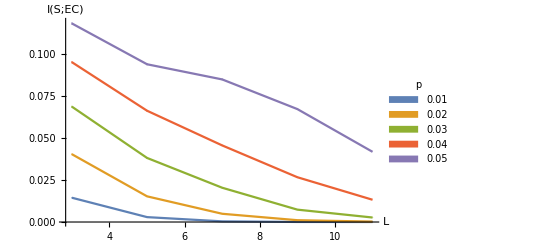

MI_w2.pdf

{{{3.,0.0023866000024},{5.,0.00027790000028},{7.,0.000024800000025},{9.,1.600000001610^-6},{11.,3.000000003010^-7}},{{3.,0.00909750009},{5.,0.0021644000022},{7.,0.000405400004},{9.,0.0000713000007},{11.,0.000013700000014}},{{3.,0.019502800019},{5.,0.00691200007},{7.,0.0021051000021},{9.,0.000608000006},{11.,0.00019450000019}},{{3.,0.032965400032},{5.,0.015544700015},{7.,0.00647980006},{9.,0.0026711000027},{11.,0.0011877000012}},{{3.,0.0490965005},{5.,0.028472300028},{7.,0.015128500015},{9.,0.00801470008},{11.,0.00453360005}}}

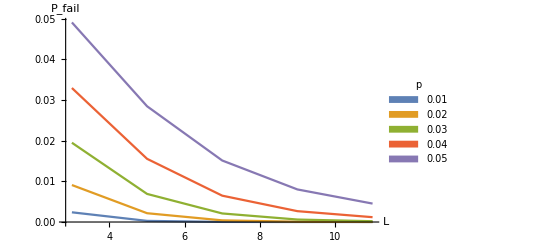

Pfail_w2.pdf

{{0.01,3.,3.,0.233588,9.51×10^-8,0.0584726},{0.01,5.,3.,0.020458,2.92×10^-8,0.0049434},{0.01,7.,3.,0.0368854,2.68×10^-8,0.0043856},{0.01,9.,3.,0.00519944,5.39×10^-9,0.0004316},{0.01,11.,3.,0.000989499,1.29×10^-9,0.0000671},{0.02,3.,3.,0.335684,1.×10^-7,0.114347},{0.02,5.,3.,0.061015,6.45×10^-8,0.020639},{0.02,7.,3.,0.109603,7.14×10^-8,0.0177189},{0.02,9.,3.,0.0324689,2.41×10^-8,0.0037178},{0.02,11.,3.,0.00975441,8.76×10^-9,0.0008404},{0.03,3.,3.,0.386078,9.03×10^-8,0.166826},{0.03,5.,3.,0.108745,8.89×10^-8,0.0474813},{0.03,7.,3.,0.232023,1.59×10^-7,0.0420669},{0.03,9.,3.,0.0985687,5.06×10^-8,0.0132858},{0.03,11.,3.,0.0406386,2.68×10^-8,0.0043919},{0.04,3.,3.,0.40928,7.57×10^-8,0.217011},{0.04,5.,3.,0.154669,9.82×10^-8,0.0844252},{0.04,7.,3.,0.286019,9.13×10^-8,0.0727297},{0.04,9.,3.,0.20565,7.59×10^-8,0.0331808},{0.04,11.,3.,0.112697,,0.0150664},{0.05,3.,3.,0.413209,6.04×10^-8,0.264802},{0.05,5.,3.,0.193342,9.37×10^-8,0.129787},{0.05,7.,3.,0.264034,1.45×10^-7,0.115548},{0.05,9.,3.,0.351354,9.03×10^-8,0.0673807},{0.05,11.,3.,0.240566,,0.0396381}}

{{{3.,0.23360.0006},{5.,0.020460.00034},{7.,0.036890.00033},{9.,0.005200.00015},{11.,0.000990.00007}},{{3.,0.33570.0006},{5.,0.06100.0005},{7.,0.10960.0005},{9.,0.032470.00031},{11.,0.009750.00019}},{{3.,0.38610.0006},{5.,0.10870.0006},{7.,0.23200.0008},{9.,0.09860.0004},{11.,0.040640.00033}},{{3.,0.40930.0006},{5.,0.15470.0006},{7.,0.28600.0006},{9.,0.20570.0006},{11.,0.1126972 √}},{{3.,0.41320.0005},{5.,0.19330.0006},{7.,0.26400.0008},{9.,0.35140.0006},{11.,0.2405662 √}}}

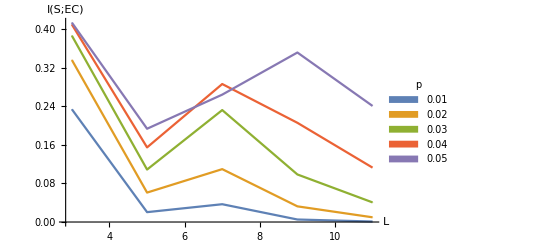

MI_w3.pdf

{{{3.,0.0584726006},{5.,0.00494340005},{7.,0.00438560004},{9.,0.000431600004},{11.,0.0000671000007}},{{3.,0.11434730010},{5.,0.020639000020},{7.,0.017718900017},{9.,0.00371780004},{11.,0.000840400008}},{{3.,0.16682560014},{5.,0.0474813005},{7.,0.0420669004},{9.,0.013285800013},{11.,0.00439190004}},{{3.,0.21701070017},{5.,0.0844252008},{7.,0.0727297007},{9.,0.033180800032},{11.,0.015066400015}},{{3.,0.26480170019},{5.,0.12978710011},{7.,0.11554800010},{9.,0.0673807006},{11.,0.0396381004}}}

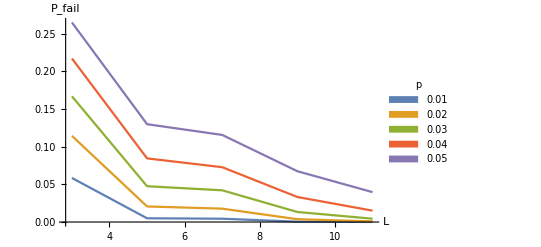

Pfail_w3.pdf

{{0.01,5.,4.,0.550399,8.31×10^-8,0.139494},{0.01,7.,4.,0.0431134,4.85×10^-8,0.0119192},{0.01,9.,4.,0.0685862,4.34×10^-8,0.0099234},{0.01,11.,4.,0.0138206,1.24×10^-8,0.001379},{0.02,5.,4.,0.732671,4.49×10^-8,0.260581},{0.02,7.,4.,0.10981,8.95×10^-8,0.0480967},{0.02,9.,4.,0.177667,8.45×10^-8,0.0397169},{0.02,11.,4.,0.0809034,4.51×10^-8,0.0106701},{0.03,5.,4.,0.782603,1.68×10^-8,0.365014},{0.03,7.,4.,0.168043,1.02×10^-7,0.10652},{0.03,9.,4.,0.165948,2.6×10^-7,0.0889478},{0.03,11.,4.,0.209745,7.75×10^-8,0.0352474},{0.04,5.,4.,0.764309,4.×10^-9,0.455165},{0.04,7.,4.,0.212208,9.13×10^-8,0.182548},{0.04,9.,4.,0.521695,7.77×10^-8,0.157495},{0.04,11.,4.,0.402579,9.14×10^-8,0.082189},{0.05,5.,4.,0.709774,3.17×10^-9,0.533238},{0.05,7.,4.,0.225287,7.78×10^-8,0.270285},{0.05,9.,4.,0.680323,5.03×10^-8,0.24252},{0.05,11.,4.,0.621897,,0.157669}}

{{{5.,0.55040.0006},{7.,0.04310.0004},{9.,0.06860.0004},{11.,0.013820.00022}},{{5.,0.73270.0004},{7.,0.10980.0006},{9.,0.17770.0006},{11.,0.08090.0004}},{{5.,0.782600.00026},{7.,0.16800.0006},{9.,0.16590.0010},{11.,0.20970.0006}},{{5.,0.764310.00013},{7.,0.21220.0006},{9.,0.52170.0006},{11.,0.40260.0006}},{{5.,0.709770.00011},{7.,0.22530.0006},{9.,0.68030.0004},{11.,0.6218972 √}}}

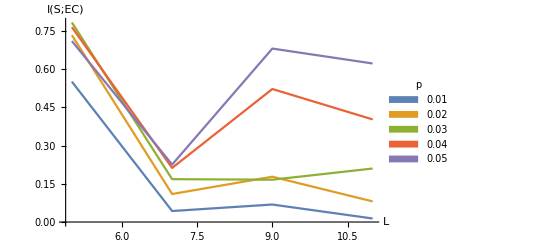

MI_w4.pdf

{{{5.,0.13949400012},{7.,0.011919200012},{9.,0.009923400010},{11.,0.0013790000014}},{{5.,0.26058110019},{7.,0.0480967005},{9.,0.0397169004},{11.,0.010670100011}},{{5.,0.36501400023},{7.,0.10651990010},{9.,0.0889478008},{11.,0.035247400034}},{{5.,0.45516500025},{7.,0.18254790015},{9.,0.15749500013},{11.,0.0821890008}},{{5.,0.53323840025},{7.,0.27028540020},{9.,0.24251960018},{11.,0.15766930013}}}

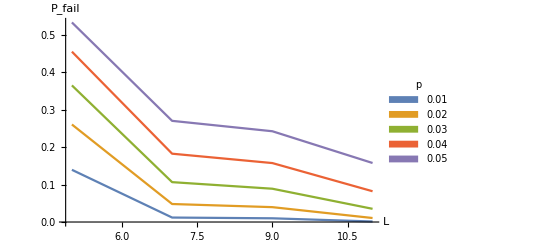

Pfail_w4.pdf

{{0.01,5.,5.,0.501635,7.89×10^-8,0.182},{0.01,7.,5.,0.6459,6.69×10^-8,0.19352},{0.01,9.,5.,0.106705,7.32×10^-8,0.0288206},{0.01,11.,5.,0.124453,6.43×10^-8,0.0216369},{0.02,5.,5.,0.58834,3.11×10^-8,0.332308},{0.02,7.,5.,0.772886,1.87×10^-8,0.354685},{0.02,9.,5.,0.25588,9.13×10^-8,0.106594},{0.02,11.,5.,0.352978,9.23×10^-8,0.082109},{0.03,5.,5.,0.567242,6.93×10^-9,0.456373},{0.03,7.,5.,0.73829,2.24×10^-9,0.486653},{0.03,9.,5.,0.126791,3.57×10^-7,0.212819},{0.03,11.,5.,0.5914,7.16×10^-8,0.17755},{0.04,5.,5.,0.506966,5.3×10^-9,0.557994},{0.04,7.,5.,0.642703,8.88×10^-9,0.593039},{0.04,9.,5.,0.929065,0.000041,0.335511},{0.04,11.,5.,0.719072,4.02×10^-8,0.292143},{0.05,5.,5.,0.43476,1.72×10^-8,0.641443},{0.05,7.,5.,0.529971,2.68×10^-8,0.67896},{0.05,9.,5.,0.445947,6.77×10^-9,0.461348},{0.05,11.,5.,0.791505,,0.42259}}

{{{5.,0.50160.0006},{7.,0.64590.0005},{9.,0.10670.0005},{11.,0.12450.0005}},{{5.,0.588340.00035},{7.,0.772890.00027},{9.,0.25590.0006},{11.,0.35300.0006}},{{5.,0.567240.00017},{7.,0.738290.00009},{9.,0.12680.0012},{11.,0.59140.0005}},{{5.,0.506970.00015},{7.,0.642700.00019},{9.,0.9290.013},{11.,0.71910.0004}},{{5.,0.434760.00026},{7.,0.529970.00033},{9.,0.445950.00016},{11.,0.7915052 √}}}

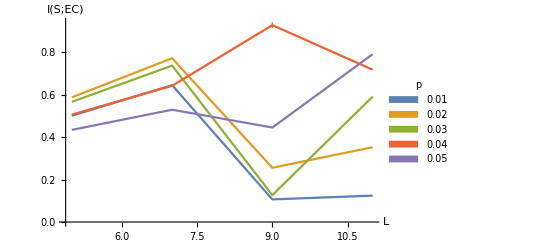

MI_w5.pdf

{{{5.,0.18200030015},{7.,0.19351990016},{9.,0.028820600028},{11.,0.021636900021}},{{5.,0.33230820022},{7.,0.35468530023},{9.,0.10659350010},{11.,0.0821090008}},{{5.,0.45637310025},{7.,0.48665250025},{9.,0.21281870017},{11.,0.17755020015}},{{5.,0.55799350025},{7.,0.59303880024},{9.,0.33551140022},{11.,0.29214260021}},{{5.,0.64144250023},{7.,0.67896030022},{9.,0.46134800025},{11.,0.42259040024}}}

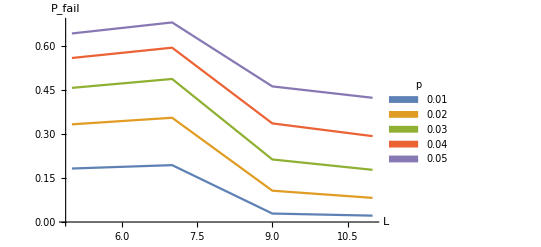

Pfail_w5.pdf

```mathematica
sDataw2=Select[sData,#[[3]]==2&]
Dataw2=Apply[Around,Transpose[{sDataw2[[;;,4]],2*Sqrt[sDataw2[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sDataw2[[;;,2]],Dataw2}],5]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw2[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["MI_w2.pdf",plot]

Dataw2=Apply[Around,Transpose[{sDataw2[[;;,6]],sDataw2[[;;,6]]*(1-sDataw2[[;;,6]])/(10^7)}],1];
DataPlot=Partition[Transpose[{sDataw2[[;;,2]],Dataw2}],5]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw2[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["Pfail_w2.pdf",plot]


sDataw3=Select[sData,#[[3]]==3&]
Dataw3=Apply[Around,Transpose[{sDataw3[[;;,4]],2*Sqrt[sDataw3[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sDataw3[[;;,2]],Dataw3}],5]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw3[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["MI_w3.pdf",plot]

Dataw3=Apply[Around,Transpose[{sDataw3[[;;,6]],sDataw3[[;;,6]]*(1-sDataw3[[;;,6]])/(10^7)}],1];
DataPlot=Partition[Transpose[{sDataw3[[;;,2]],Dataw3}],5]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw3[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["Pfail_w3.pdf",plot]


sDataw4=Select[sData,#[[3]]==4&]
Dataw4=Apply[Around,Transpose[{sDataw4[[;;,4]],2*Sqrt[sDataw4[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sDataw4[[;;,2]],Dataw4}],4]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw4[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["MI_w4.pdf",plot]

Dataw4=Apply[Around,Transpose[{sDataw4[[;;,6]],sDataw4[[;;,6]]*(1-sDataw4[[;;,6]])/(10^7)}],1];
DataPlot=Partition[Transpose[{sDataw4[[;;,2]],Dataw4}],4]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw4[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["Pfail_w4.pdf",plot]


sDataw5=Select[sData,#[[3]]==5&]
Dataw5=Apply[Around,Transpose[{sDataw5[[;;,4]],2*Sqrt[sDataw5[[;;,5]]]}],1];
DataPlot=Partition[Transpose[{sDataw5[[;;,2]],Dataw5}],4]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw5[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["MI_w5.pdf",plot]

Dataw5=Apply[Around,Transpose[{sDataw5[[;;,6]],sDataw5[[;;,6]]*(1-sDataw5[[;;,6]])/(10^7)}],1];
DataPlot=Partition[Transpose[{sDataw5[[;;,2]],Dataw5}],4]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sDataw5[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["Pfail_w5.pdf",plot]
```